### Parameters

```mathematica
Ω=.;tMax=.;pulseList=xy8;τ=.
```

### Background code

#### Pulses

{angle of rotation, vector of rotation or time of rotation}
vector of rotation = {x, y, z}

```mathematica
ramsey={{0,τ}};
spinEcho={{0,τ},{π,"x"},{0,τ}};
piPulse={{π,"x"}};
xy8={{0,τ},{π,"x"},{0,τ},{π,"y"},{0,τ},{π,"x"},{0,τ},{π,"y"},{0,τ},{π,"y"},{0,τ},{π,"x"},{0,τ},{π,"y"},{0,τ},{π,"x"},{0,τ}};
xy16=Join[xy8[[;;-2]],xy8];
vecName={"x"->{1,0,0},"y"->{0,1,0},"z"->{0,0,1},"-x"->{-1,0,0},"-y"->{0,-1,0},"-z"->{0,0,-1}};
```

#### Hamiltonians

```mathematica
σ={σx,σy,σz}=(PauliMatrix[#1]&)/@{1,2,3};σp=σx+ⅈ σy;σm=σx-ⅈ σy;
a=.;b=.;conj=Complex[a_,b_]->Complex[a,-b];
hc[x_]:=Transpose[x]/.conj;
Hc[vec_]:=If[SameQ[vec,0],({{0, 0}, {0, 0}}),1/2 Ω ∑_(n=1)^3 σ⟦n⟧ Normalize[vec]⟦n⟧]
```

#### Time Steps

```mathematica
findTime[pulse_]:=If[SameQ[pulse[[1]],0],{0,pulse[[2]]},{0,pulse[[1]]/Ω}]
findTimes[pulseList_]:=Accumulate[Flatten[findTime[pulseList[[#]]]&/@Range@Length[pulseList]]];
findτ0[pulseList_]:=If[!FreeQ[findTimes[pulseList][[-1]],τ],N[τ/.Solve[tMax==findTimes[pulseList][[-1]],τ]⟦1⟧],tMax]
```

#### Unitary matrices

```mathematica
Uc[t_,t0_,tf_,vec_]:=Simplify[MatrixExp[-ⅈ Hc[vec] Piecewise[{{t-t0,t0<t<tf},{tf-t0,t≥tf}}]],Assumptions->Ω>0];createUnitary[t_,pulseList_,τ0_:τ]:=Module[{tStarts,tEnds,vecs,tsI,vecName,pulses},
pulses=Length[pulseList];
vecName={"x"->{1,0,0},"y"->{0,1,0},"z"->{0,0,1},"-x"->{-1,0,0},"-y"->{0,-1,0},"-z"->{0,0,-1}};vecs=Replace[pulseList⟦All,2⟧/.vecName,i_/;Not[ListQ[i]]->0,1];
tsI=findTimes[pulseList];
tsI=tsI/.τ->τ0;Simplify[Dot@@Reverse[MapThread[Hold[Uc],{ConstantArray[t,pulses],tsI[[1;;;;2]],tsI⟦2;;;;2⟧,vecs}]]]]
```

```mathematica
findQ[pulseList_]:=Module[{Q,tFs},
Q={IdentityMatrix[2]};
tFs=findTimes[pulseList][[2;;;;2]];
Do[Q=Append[Q,If[Length[pulseList]==1,createUnitary[tFs[[n]],pulseList],Reverse[createUnitary[tFs[[n]],pulseList]]⟦n⟧].Q⟦-1⟧],{n,1,Length[pulseList]}];
Q]
```

```mathematica
Q=ReleaseHold[findQ[pulseList]];
Λ[i_,j_,l_]:=1/2 Tr[hc[Q[[l+1]]].σ[[i]].Q[[l+1]].σ[[j]]];
Λ[l_]:=Table[Λ[i,j,l],{i,1,3},{j,1,3}]
```

```mathematica
Rz[j_,l_,ω_]:=Module[{fl,gl,ti,tf,Ωl,θl,vec,σϕ},{ti,tf}=findTimes[pulseList][[2 l-1;;2l]];
vec=Replace[pulseList⟦l,2⟧/.vecName,i_/;Not[ListQ[i]]->{1,0,0}];
σϕ=Sum[vec[[n]]σ[[n]],{n,1,3}];
θl=pulseList[[l,1]];
Ωl=θl/(tf-ti);
fl=Exp[ⅈ ω (tf-ti)]Cos[θl]-1;
gl=Exp[ⅈ ω (tf-ti)]Sin[θl];
ω/(ω^2-Ωl^2)(KroneckerDelta[3,j](ⅈ Ωl gl-ω fl)+(Ωl fl-ⅈ ω gl)Tr[σϕ.σz.σ[[j]]])]
```

```mathematica
Rz[l_,ω_]:=Table[Rz[j,l,ω],{j,1,3}]
```

```mathematica
Rz[ω_]=Module[{tis},tis=findTimes[pulseList][[1;;;;2]];
Sum[Exp[ⅈ ω tis[[l]]](Rz[l,ω].Λ[l-1]),{l,1,Length@pulseList}]];
```

```mathematica
FzLim[ω_]=FullSimplify[Total[((#/.conj)#)&/@Limit[Rz[ω],Ω->∞]]]
```

4 (2 Sin[(τ ω)/2]-2 (Sin[(3 τ ω)/2]-Sin[(5 τ ω)/2]+Sin[(7 τ ω)/2])+Sin[(9 τ ω)/2])^2

```mathematica
Fz[ω_]=Total[((#/.conj)#)&/@Rz[ω]];
```

### Results

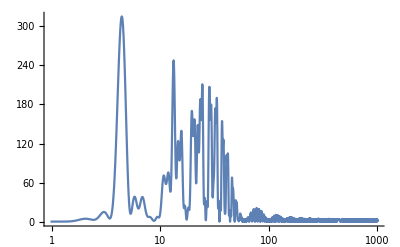

```mathematica
(*Plot[FzLim[ω]//.{τ->Limit[findτ0[pulseList],Ω->∞],tMax->1},{ω,0,100π},Ticks->{Range[0,100π,2π],Automatic},PlotRange->All]*)
LogLinearPlot[Fz[2π f]//.{τ->findτ0[pulseList],tMax->1,Ω->20 2π},{f,0,1000},PlotRange->All]
```